```mathematica
Manipulate[
Table[N[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Cos[k θ]],{θ,0,2Pi,Pi/7}],
{n,2,10},{k,0,9,1}
]
```

```mathematica
Manipulate[
Show[
PolarPlot[Sec[x]/(1+Tan[x]^n)^(1/n),{x,0,π/2}],
PolarPlot[Sec[π-x]/(1+Tan[π-x]^n)^(1/n),{x,π/2,π}],
PolarPlot[Sec[x-π]/(1+Tan[x-π]^n)^(1/n),{x,π,3π/2}],
PolarPlot[Sec[2π-x]/(1+Tan[2π-x]^n)^(1/n),{x,3π/2,2π}]
],{n,2,10}
]
```

```mathematica
Manipulate[
Table[N[4Cos[θ]^m(1+Tan[θ]^n)^(m/n)Cos[m θ]Cos[k θ]],{θ,0,2Pi,Pi/7}],
{n,2,10},{k,0,9,1},{m,0,9,1}
]
```

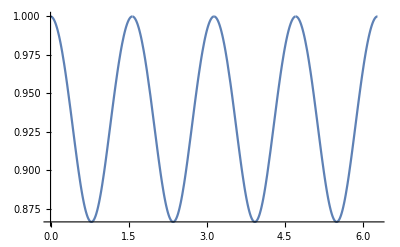

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -4.996×10^-16 and 1.32773×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.5707}. NIntegrate obtained 2.77556×10^-17 and 2.79345×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -5.55112×10^-16 and 1.88534×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

I1 <|0→-0.429338,1→5.89806×10^-17,2→-2.43729×10^-16|>

I2 <|{0,0}→6.28319,{1,0}→-4.996×10^-16,{2,0}→-8.04912×10^-16,{0,1}→-3.22659×10^-16,{1,1}→2.93782,{2,1}→-2.91434×10^-16,{0,2}→-5.75928×10^-16,{1,2}→-8.30065×10^-16,{2,2}→2.94934|>

I3 <|{0,0}→0.,{1,0}→2.77556×10^-17,{2,0}→5.55112×10^-17,{0,1}→0.,{1,1}→1.56125×10^-16,{2,1}→2.15106×10^-16,{0,2}→0.,{1,2}→3.55618×10^-17,{2,2}→-3.72966×10^-16|>

I4 <|{0,0}→6.28319,{1,0}→-5.55112×10^-16,{2,0}→5.55112×10^-17,{0,1}→-3.22659×10^-16,{1,1}→3.36805,{2,1}→-3.26128×10^-16,{0,2}→-5.75928×10^-16,{1,2}→-7.66748×10^-16,{2,2}→3.36188|>

I5 <|{0,0}→0.,{1,0}→1.66533×10^-16,{2,0}→-6.93889×10^-17,{0,1}→0.,{1,1}→-2.04697×10^-16,{2,1}→-2.36356×10^-16,{0,2}→0.,{1,2}→6.93889×10^-17,{2,2}→5.0307×10^-17|>

I6 <|1→-2.25514×10^-17,2→-1.73472×10^-18|>

I7 <|{0,1}→1.47451×10^-16,{1,1}→1.56125×10^-16,{2,1}→-1.249×10^-16,{0,2}→-2.08167×10^-17,{1,2}→1.59595×10^-16,{2,2}→-3.72966×10^-16|>

I8 <|{0,1}→0.,{1,1}→2.93782,{2,1}→1.8735×10^-16,{0,2}→0.,{1,2}→1.80411×10^-16,{2,2}→2.55909|>

I9 <|{0,1}→1.47451×10^-16,{1,1}→-2.04697×10^-16,{2,1}→-2.91434×10^-16,{0,2}→-2.08167×10^-17,{1,2}→-1.249×10^-16,{2,2}→5.0307×10^-17|>

I10 <|{0,1}→0.,{1,1}→3.36805,{2,1}→2.42861×10^-16,{0,2}→0.,{1,2}→2.77556×10^-17,{2,2}→3.87825|>

NSolve::svars: Equations may not give solutions for all "solve" variables.

Number of variables 10 Number of equations 10 4M+2= 10

{{ϕ[1.]→-1.02021×10^6+14.6346 ϕ[0.],C1[1.]→2.83889×10^-27-0.872261 A1[1.]+1.58108×10^-18 A1[2.]-9.93673×10^-17 B1[1.]-1.10173×10^-16 B1[2.]-2.56278×10^-16 ϕ[0.],C1[2.]→-3.06207×10^-27+4.79675×10^-17 A1[1.]-0.877289 A1[2.]+7.42543×10^-18 B1[1.]+1.20813×10^-16 B1[2.]+1.06097×10^-15 ϕ[0.],D1[1.]→-5.22595×10^-28-9.93673×10^-17 A1[1.]-3.88269×10^-17 A1[2.]-0.872261 B1[1.]-8.04507×10^-18 B1[2.]+9.79885×10^-17 ϕ[0.],D1[2.]→-2.20239×10^-29-6.92426×10^-17 A1[1.]+1.07548×10^-16 A1[2.]-4.02762×10^-17 B1[1.]-0.659858 B1[2.]+6.54599×10^-18 ϕ[0.]}}

```mathematica
Block[
{func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,var,soln},
q=5.673*10^(-5);
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=2;
n=3.41;
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
Print[Plot[func[θ,n],{θ,0,2π}]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
If[
k≥1,
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
]
];
Print["I1 ",I1];Print["I2 ",I2];Print["I3 ",I3];Print["I4 ",I4];Print["I5 ",I5];
Print["I6 ",I6];Print["I7 ",I7];Print["I8 ",I8];Print["I9 ",I9];Print["I10 ",I10];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}]==0,{m,1,M}],{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}]==0,{m,1,M}],{k,1,M}];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
soln=SetPrecision[NSolve[Join[eq1,eq2,eq3,eq4],var],MachinePrecision];
Print["Number of variables ",Length[var]," Number of equations ",Length[Join[eq1,eq2,eq3,eq4]]," 4M+2= ",4M+2];
Print[soln];
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -5.55112×10^-16 and 5.73259×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.5707}. NIntegrate obtained 2.77556×10^-16 and 1.37531×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -6.66134×10^-16 and 5.93942×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Number of variables 14 Number of equations 14 4M+2= 14

{{ϕ[0]→-1/10,ϕ[1]→-1.02021×10^6,A1[1]→-11/5,A1[2]→2.6584×10^-17,A1[3]→-0.667809,B1[1]→-1.77974×10^-16,B1[2]→7.83498×10^-17,B1[3]→-6.58584×10^-17,C1[1]→2.1214,C1[2]→-7.21267×10^-17,C1[3]→0.611176,D1[1]→1.91977×10^-16,D1[2]→-1.83041×10^-17,D1[3]→7.1628×10^-17}}

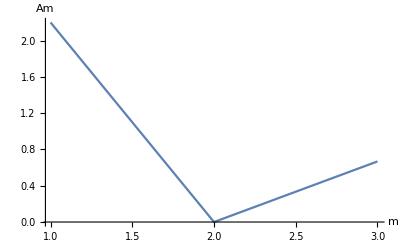

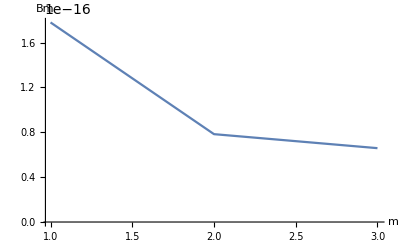

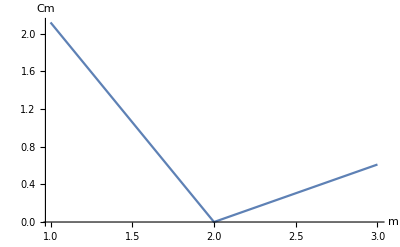

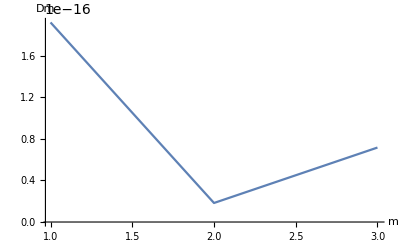

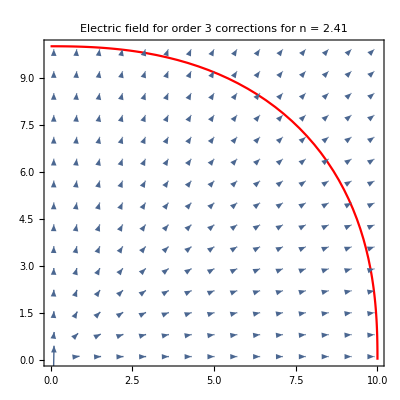

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,var,soln},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=3; (* The number of coefficients *)
n=2.41; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
soln=FindInstance[Join[eq1,eq2,eq3,eq4],var,Reals,WorkingPrecision->100,RandomSeeding->Automatic];
Print["Number of variables ",Length[var]," Number of equations ",Length[Join[eq1,eq2,eq3,eq4]]," 4M+2= ",4M+2];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[C1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[D1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
Er[x_,y_]:=Part[-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Et[x_,y_]:=Part[(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained -1.94289×10^-16 and 1.38764×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {6.2831611214131084832670761514128443536719714757055044174194335938}. NIntegrate obtained 2.35706×10^-16 and 1.22215×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.33784}. NIntegrate obtained -1.35308×10^-15 and 4.72056×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Number of variables 14 Number of equations 14 4M+2= 14

{{ϕ[0]→-29/10,ϕ[1]→-1.02025×10^6,A1[1]→21/10,A1[2]→-6.65279×10^-17,A1[3]→0.476956,B1[1]→8.61924×10^-16,B1[2]→-1.59491×10^-17,B1[3]→9.38787×10^-16,C1[1]→-1.90288,C1[2]→-1.92731×10^-17,C1[3]→-0.429669,D1[1]→-4.65585×10^-16,D1[2]→4.98313×10^-17,D1[3]→-3.38743×10^-16}}

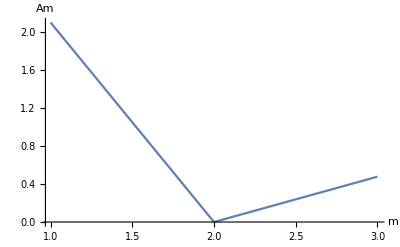

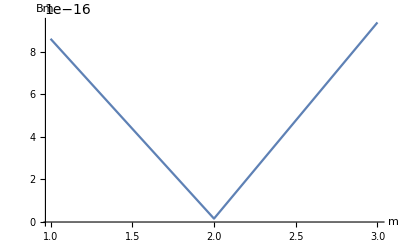

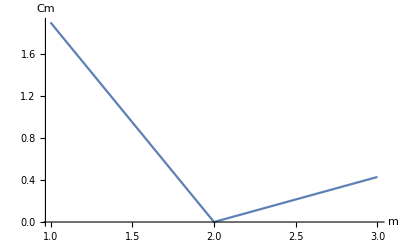

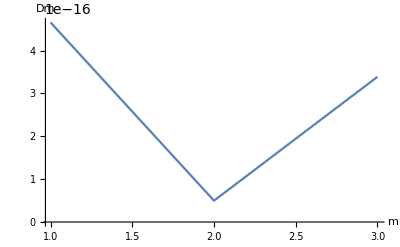

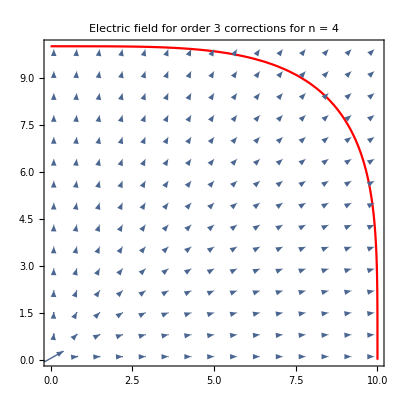

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,var,soln},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=3; (* The number of coefficients *)
n=4; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
soln=FindInstance[Join[eq1,eq2,eq3,eq4],var,Reals,WorkingPrecision->100,RandomSeeding->Automatic];
Print["Number of variables ",Length[var]," Number of equations ",Length[Join[eq1,eq2,eq3,eq4]]," 4M+2= ",4M+2];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[C1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[D1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
Er[x_,y_]:=Part[-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Et[x_,y_]:=Part[(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.89606}. NIntegrate obtained -1.30104×10^-15 and 4.22719×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Number of variables 2 Number of equations 2 4M+2= 2

{{ϕ[0]→-11/5,ϕ[1]→-1.16521×10^17}}

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

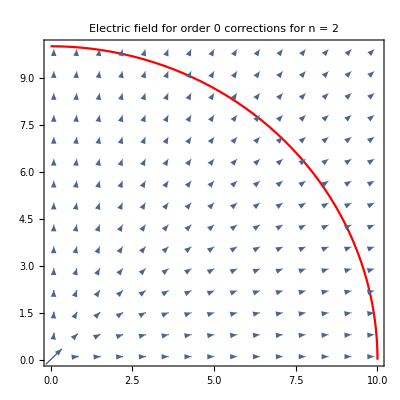

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,var,soln},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=0; (* The number of coefficients *)
n=2; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
soln=FindInstance[Join[eq1,eq2,eq3,eq4],var,Reals,WorkingPrecision->100,RandomSeeding->Automatic];
Print["Number of variables ",Length[var]," Number of equations ",Length[Join[eq1,eq2,eq3,eq4]]," 4M+2= ",4M+2];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[C1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[D1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
Er[x_,y_]:=Part[-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Et[x_,y_]:=Part[(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```